Do the following tasks using Mathematica.

(a) Solve the differential equation:

xy’ = 4y

Plot multiple solutions of the differential equation with values of constants
c=-2,-1,0,1,2 in a single graph

```mathematica
DSolve[x y'[x]== 4 y[x],y[x],x]
```

{{y[x]→x^4 C[1]}}

```mathematica
sol = y[x]/.%1/.C[1]-> a
```

{a x^4}

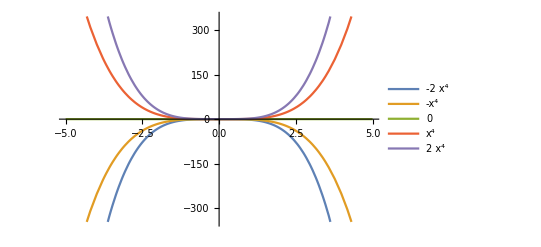

```mathematica
Plot[Evaluate[Table[sol,{a,-2,2}]],{x,-5,5},PlotLegends->"Expressions"]
```

(b)

y’’ − 10y’ + 25y = 0 ; y(0) = 1 , y’(1) = 0 Find the value of y(2)

```mathematica
DSolve[{y''[t] - 10 y'[t] + 25 y[t] == 0 , y[0] ==1 , y'[1] == 0}, y[t], t]
```

{{y[t]→-1/6 ⅇ^(5 t) (-6+5 t)}}

```mathematica
y[t]/.%4/.t-> 2//N
```

{-14684.3}

```mathematica
ClearAll["Global`*"]
```

(c) Plot the numerical solution of the differential equation for 0 ≤ t ≤ 50:

x’’ + 0.15x’ − x + x^3 = 0.3 cost , x(0) = −1 , x’(0) = 1

```mathematica
NDSolve[{x''[t] + 0.15  x'[t] - x[t] + x[t]^3 == 0.3  Cos[t], x[0] == -1, x'[0] == 1},x[t],{t,0,50}]
```

{{x[t]→InterpolatingFunction[…][t]}}

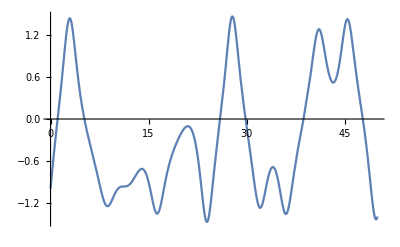

```mathematica
Plot[x[t]/.%7,{t,0,50},PlotRange->Full]
```